```mathematica
<<peeters`;
peeters`setGitDir["../project/figures/phy452-basicstatmech"]
```

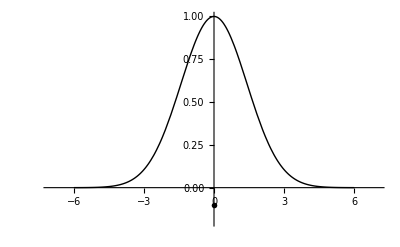

```mathematica
ClearAll[p, r, basicStatMechLecture4Fig1]
r = 6;
p = Plot[ Exp[-x^2/4], {x, -r,r},
 PlotStyle-> {Thick, Black},
PlotRange->{{-r-1, r+1}, {-0.2, 1}},
Ticks -> None,
AxesLabel-> {MaTeX["\\mathbf{v}_i"], MaTeX["P_{N_c}(\\mathbf{v}_i)"]}
];

basicStatMechLecture4Fig1 = Show[{p, Graphics[Text[MaTeX["\\mathbf{v}_i(0)"], {0,-0.1}]]}]
```

```mathematica
peeters`exportForLatex["basicStatMechLecture4Fig1", basicStatMechLecture4Fig1]
```

{basicStatMechLecture4Fig1.eps,basicStatMechLecture4Fig1pn.png}